-Graphics3D-

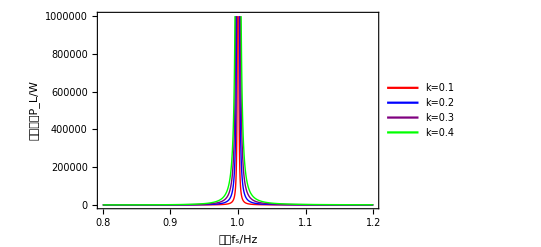

```mathematica
Clear[w,Rl,g,Lp,Ls,Cp,Cs,k];
Uin=72;
Rl=10;
Lp=Ls=116.86×10^-6;
Pout=(k^2*Ls*Rl*Uin^2*w^6)/(Lp*(Rl^2*w^2*(w^2-1)^2+Ls^2*w^2*((k^2-1)*w^4+2*w^2-1)^2));

(*ContourPlot3D[Pout==(k^2*Ls*Rl*Uin^2*w^6)/(Lp*(Rl^2*w^2*(w^2-1)^2+Ls^2*w^2*((k^2-1)*w^4+2*w^2-1)^2)),{k,0,1},{w,0.8,1.2},{Pout,0,1000}]*)

Plot[Evaluate@Table[Pout,{k,0.1,0.4,0.1}],{w,0.8,1.2},
PlotRange->{0,1000000},
Frame->True,
FrameLabel->{Style["(:9891:7387f)_s/Hz",Black],Style["(:8f93:51fa:529f:7387P)_L/W",Black]},
PlotLegends->Placed[{"k=0.1","k=0.2","k=0.3","k=0.4"},{0.88,0.7}],
(*PlotLabel->Style["不同耦合系数k下，(:8f93:51fa:529f:7387P)_L(:4e0e:9891:7387f)_s的关系",Black,Bold],*)
PlotStyle->{{Red,Thick},{Blue,Thick},{Purple,Thick},{Green,Thick},{Orange,Thick}}]
```

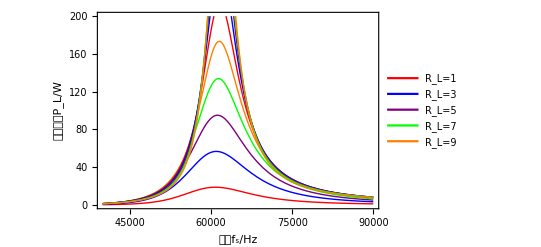

```mathematica
Clear[w,Rl,g,Lp,Ls,Cp,Cs,k,Uout];
Lp=Ls=30×10^-6;
Cp=Cs=220×10^-9;
Uin=20;
fr=1.0/(2*π*√(Lp*Cp));
k=0.4;
M=√(Lp×Ls)×k;
Rp=0.05;
Rs=0.05;

s=2*π*w*I;
R1=Rp+(s*Lp+1/(s*Cp));
R2=Rs+Rl+(s*Ls+1/(s*Cs));
Rf=(s*M)^2/R2;
Ip=Uin/(R1+Rf);
Is=s*M/R2*Ip;
Uout=Is*Rl;
Pout=Is*Uout;
Pout=Sqrt[ComplexExpand[Re[FullSimplify[Pout]]]^2+ComplexExpand[Im[FullSimplify[Pout]]]^2];
Plot[Evaluate@Table[Pout,{Rl,1,20,2}],{w,40000,90000},
PlotRange->{0,200},
Frame->True,
FrameLabel->{Style["(:9891:7387f)_s/Hz",Black],Style["(:8f93:51fa:529f:7387P)_L/W",Black]},
PlotLegends->Placed[{"R_L=1","R_L=3","R_L=5","R_L=7","R_L=9"},{0.88,0.7}],
(*PlotLabel->Style["(:4e0d:540c:8d1f:8f7d:7535:963bR)_L下，(:8f93:51fa:529f:7387P)_L(:4e0e:9891:7387f)_s的关系",Black,Bold],*)
PlotStyle->{{Red,Thick},{Blue,Thick},{Purple,Thick},{Green,Thick},{Orange,Thick}}]
```